# Chapter 5: Proposal for a photon-photon gate and error analysis

## Author: Bruno Ortega Goes

## Preamble

```mathematica
PlotsPath = "/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap5/";
overleafPath="/Users/brunogoes/Dropbox/Aplicativos/Overleaf/00Bruno-Goes-ThesisDraft/Figures/Chap5/";

(*To easily insert a label*)
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};

AlphabetLabelling[x_,xpos_:0.1,ypos_:0.9] := Text["("<>ToString@x<>")",Scaled[{xpos,ypos}]];
```

We define the ordered Pauli basis:

```mathematica
𝒫 = Table[kron[i,j],{i,{σ0,σx,σy,σz}},{j,{σ0,σx,σy,σz}}]//mf;
```

((1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)
(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)
(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1))

```mathematica
Clear[Fave];
Fave[Ureal_,Uideal_]:=(Tr[Ureal†.Ureal]+Abs[Tr[Uideal†.Ureal]]^2)/20
```

## Pulse shape:Decreasing pulse

Through this section I apply the formalism assuming a decreasing exponential pulse.

## Input and output pulse shapes

```mathematica
Intensity[funcoft_]:=funcoft funcoft*//cf
```

```mathematica
Clear[ξdec,γ,Γ,ω0];
ξdec[t_] := √(Γ/2)Exp[-(Γ/4)t];
InputIntensityDec=Intensity[ξdec[t]];

Assuming[Γ>0,Integrate[ξdec[t] ξdec[t]*//cf, {t,0,∞}]]
```

1

```mathematica
Clear[ξdectilde];
ξdectilde[t_] :=ⅇ^(-(γ t)/2)Integrate[ⅇ^((γ/2)s)ξdec[s],{s,0,t}] ;
ξdectilde[t]
```

-(2 √2 ⅇ^(-(t γ)/2) (-1+ⅇ^(1/4 t (2 γ-Γ))) √Γ)/(-2 γ+Γ)

```mathematica
(*Computing the output shape*)
Υdec[t_]:=γ ξdectilde[t]-ξdec[t]
OutputIntensityDec=Intensity[Υdec[t]];
Assuming[{Γ>0 && γ>0},Integrate[Υdec[t] Υdec[t]*//cf, {t,0,∞}]]
```

1

```mathematica
Υdec[t]//cf
```

(ⅇ^(-1/4 t (2 γ+Γ)) √Γ (4 ⅇ^((t Γ)/4) γ-ⅇ^((t γ)/2) (2 γ+Γ)))/(√2 (-2 γ+Γ))

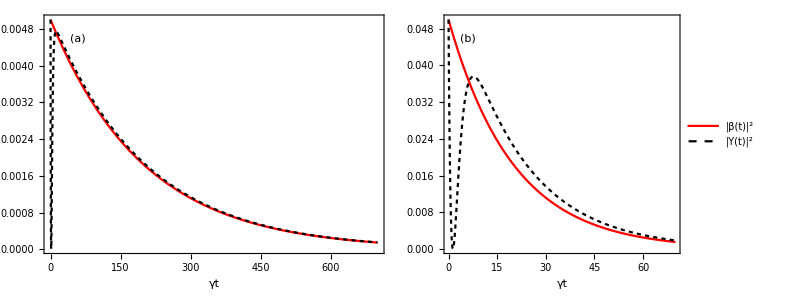

```mathematica
γ=1;

IntensityCurvesLines={{Red,Automatic},{Black,Dashing[{.01}]}};

Grid[
{
{fig1a=Plot[
{InputIntensityDec/.Γ->10^-2, OutputIntensityDec/.Γ->10^-2},{t,0,7 Γ^-1}/.Γ->10^-2,
Frame->True,
PlotStyle->IntensityCurvesLines,
PlotRange->All,
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"γt",None},
Epilog->AlphabetLabelling["a"]],

fig1b=Plot[{InputIntensityDec/.Γ->10^-1, OutputIntensityDec/.Γ->10^-1},{t,0,7 Γ^-1}/.Γ->10^-1,
Frame->True,
PlotStyle->IntensityCurvesLines,
PlotRange->All,
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"γt",None},
PlotLegends->legend[{"|β(t)|^2","|Υ(t)|^2"},{0.8,0.75}],
Epilog->AlphabetLabelling["b"]]}

(*Plot[

{InputIntensityDec/.Γ->1, OutputIntensityDec/.Γ->1},{t,0,7 Γ^-1}/.Γ->1,
Frame->True,
PlotStyle->IntensityCurvesLines,
PlotRange->All,
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"γt",None},
PlotLegends->legend[{"|ξ(t)|^2","|υ(t)|^2"},{0.8,0.75}],
Epilog->AlphabetLabelling["c"]]}
*)
}]
Export[overleafPath<>"Chap5DecreasingPulseShapeDiffeGammas.pdf",%];
```

## Non-monochromaticity parameter

```mathematica
m[InputOfT_,OutputOfT_]:=Module[{dummy},
dummy = InputOfT* OutputOfT//cf;
Integrate[dummy,{t,0,∞}]//cf]
```

```mathematica
Clear[γ]
mdec = m[ξdec[t],Υdec[t]]
```

-1+(4 γ)/(2 γ+Γ)

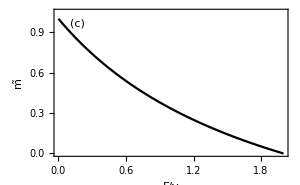

```mathematica
fig1c = Plot[mdec/.γ->1,{Γ,0,2},
Frame->True,
PlotStyle->{Black},
PlotRange->{All,{0,1.05}},
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"Γ/γ","m̃"},
Epilog->AlphabetLabelling["c"]
]
Export[overleafPath<>"Chap5DecreasingNonMonochromaticity.pdf",%];
```

Based on forthcoming analysis, the gate is implemented when m≥0.4. From this plot we have that the minimum value of Γ=0.8γ.

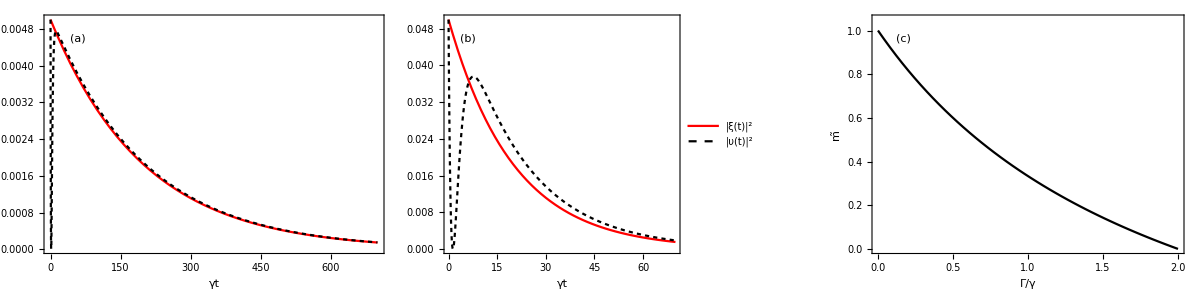

```mathematica
Grid[{{fig1a,fig1b,fig1c}}]
Export[overleafPath<>"Chap5Fig1.pdf",%];
```

```mathematica
Solve[-1+(4 γ)/(2 γ+Γ)==0.4,{Γ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Γ→0.857143}}

## Error analysis

### Analysis for the gate conditioned on spin ↑

```mathematica
GuprealOriginal =  ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -(m^2+2m-1)/2}})//cf;
GuprealOriginal/.m->1//mf;
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

The non-monochromaticity introduces a phase error to the desired gate. We parametrize this error by Exp[ⅈ ϵup] where ϵup is the gate angle error.

The real rotation, when the scattered field is not monochromatic is given by:

```mathematica
sol1=Flatten@Solve[{(m^2+2m-1)/2==ⅇ^(ⅈ ϵup)},ϵup]//cf
```

{ϵup→ConditionalExpression[2 π C[1]-ⅈ Log[1/2 (-1+m (2+m))], C[1]∈ℤ]}

Since we want ⅇ^(ⅈ ϵup)=1, C[1]=1.

```mathematica
gateUpangleerror=ⅇ^(ⅈ ϵup)/. ϵup->2π -ⅈ Log[1/2 (-1+m (2+m))]
```

ⅇ^(ⅈ (2 π-ⅈ Log[1/2 (-1+m (2+m))]))

If m=1

```mathematica
gateUpangleerror/.m->1
```

1

```mathematica
realGateAngle = 2π -ⅈ Log[1/2 (-1+m (2+m))];
```

```mathematica
imaginaryparError=Table[{m,Chop[Im[realGateAngle]]/π},{m,0,1,0.001}];
realparError=Table[{m,Chop[Re[realGateAngle]]/π},{m,0,1,0.001}];
```

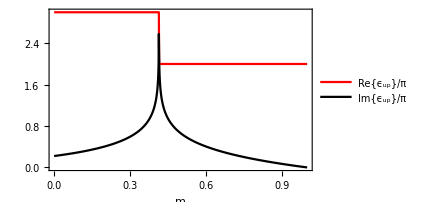

```mathematica
angleerrorUpPlot=ListLinePlot[{realparError,imaginaryparError},
PlotStyle->{{Red},{Black}},
PlotLegends->legend[{"Re{ϵ_up}/π","Im{ϵ_up}/π"},{0.8,0.35}],
FrameLabel->{"m"}]
Export[overleafPath<>"angleerrorUpPlot.pdf",angleerrorUpPlot];
```

This plot is interesting. It informs us that in order to obtain the desired CZ-gate , i.e. -Exp[ⅈ ϵup]=-1, the m-parameter must be bigger than 0.4, otherwise the real part is 3π  what would lead to the identity, -Exp[ⅈ ϵup]=1. Focusing on the part where m>0.4 we have the desired CZ-gate implemented, as the real part of ϵ_up is 2π. The error is unitary, if m=1 (monochromatic output) we obtain the desired gate,if 0.4<m<1 we have the imaginary part that is responsible for tilting the gate.

With this parametrization the gate can be written in a unitary form as:

```mathematica
Gupreal = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -ⅇ^(ⅈ ϵup)}})//cf;
Gupideal = Gupreal/.ϵup->2π//mf;
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
(Gupreal†.Gupreal//cf )==Eye[4]
(Gupreal.Gupreal†//cf )==Eye[4]
```

True

True

```mathematica
Guprealsimplified=Gupreal/. ϵup->2π -ⅈ Log[1/2 (-1+m (2+m))]//cf//mf;
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1/2 (1-m (2+m)))

1/20 (4+1/4 (5+m (2+m))^2)

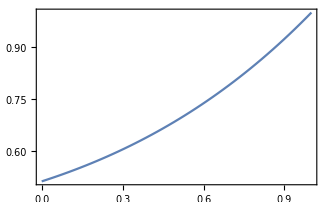

```mathematica
averagefidelityup=Fave[Gupideal,Guprealsimplified]//cf
Plot[averagefidelityup,{m,0,1}]
```

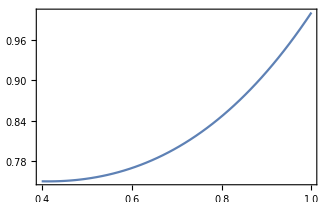

```mathematica
Plot[Tr[Guprealsimplified†.Guprealsimplified]/4,{m,0.4,1}]
```

The error matrix is given by:

```mathematica
Eup = Gupreal.Inverse[Gupideal]//mf;
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ ϵup))

Decomposing in the Pauli basis (performing PTA):

```mathematica
PTAup = Table[Tr[𝒫⟦i,j⟧.Eup]/4,{i,1,4},{j,1,4}]//cf//mf;
```

(1/4 (3+ⅇ^(ⅈ ϵup)) | 0 | 0 | 1/4 (1-ⅇ^(ⅈ ϵup))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/4 (1-ⅇ^(ⅈ ϵup)) | 0 | 0 | 1/4 (-1+ⅇ^(ⅈ ϵup)))

```mathematica
PTAupm=PTAup/. ϵup->2π -ⅈ Log[1/2 (-1+m (2+m))]//cf//mf;
```

(1/8 (5+m (2+m)) | 0 | 0 | -1/8 (-1+m) (3+m)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/8 (-1+m) (3+m) | 0 | 0 | 1/8 (-1+m) (3+m))

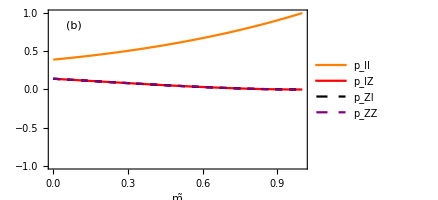

```mathematica
Plot[Evaluate[DeleteCases[Flatten[Abs[PTAupm]^2],0]],{m,0,1},Frame->True,BaseStyle->14,
(*PlotRange->plotrangeamplitudes,*)
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{0,-1},
FrameLabel->{"m̃",None},
PlotStyle->{Orange,{Red},{Black,Dashed},{Purple,Dashed}},
PlotLegends->legend[{"p_II","p_IZ","p_ZI","p_ZZ"},{0.7,0.23},LegendLayout->{"Row",2}],
Epilog->Text["(b)",Scaled[{0.1,0.9}]]
(*Epilog->AlphabetLabelling["c"]*)]
```

### Analysis for the gate conditioned on spin ↓

```mathematica
GdwrealOriginal =  ({{1, 0, 0, 0}, {0, -m, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, (m^2+1)/2}})//cf;
GdwrealOriginal/.m->1//mf;
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
solϵdw = Flatten@Solve[ⅇ^(ⅈ ϵdw)==m,ϵdw]//cf
```

{ϵdw→ConditionalExpression[2 π C[1]-ⅈ Log[m], C[1]∈ℤ]}

```mathematica
realDownGateAngle=2 π -ⅈ Log[m]
```

2 π-ⅈ Log[m]

```mathematica
imaginaryparErrorDw=Table[{m,Chop[Im[realDownGateAngle]]/π},{m,0,1,0.001}];
realparErrorDw=Table[{m,Chop[Re[realDownGateAngle]]/π},{m,0,1,0.001}];
```

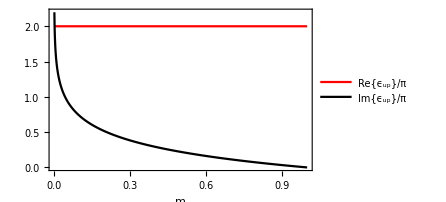

```mathematica
angleerrorDwPlot=ListLinePlot[{realparErrorDw,imaginaryparErrorDw},
PlotStyle->{{Red},{Black}},
PlotLegends->legend[{"Re{ϵ_up}/π","Im{ϵ_up}/π"},{0.8,0.35}],
FrameLabel->{"m"}]
Export[overleafPath<>"angleerrorDwPlot.pdf",angleerrorDwPlot];
```

```mathematica
solδdw = Flatten@Solve[ⅇ^(ⅈ δdw)==(m^2+1)/2,δdw]//cf
```

{δdw→ConditionalExpression[2 π C[1]-ⅈ Log[1/2 (1+m^2)], C[1]∈ℤ]}

```mathematica
anotherUnitaryerror=2 π -ⅈ Log[1/2 (1+m^2)]
```

2 π-ⅈ Log[1/2 (1+m^2)]

```mathematica
imaginaryparAnotherUnitaryErrorDw=Table[{m,Chop[Im[anotherUnitaryerror]]/π},{m,0,1,0.001}];
realparAnotherUnitaryErrorDw=Table[{m,Chop[Re[anotherUnitaryerror]]/π},{m,0,1,0.001}];
```

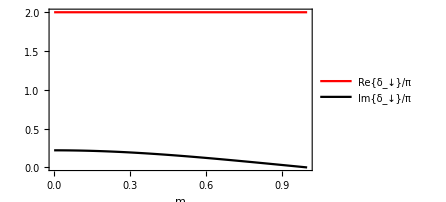

```mathematica
anotherUnitaryerrorDwPlot=ListLinePlot[{realparAnotherUnitaryErrorDw,imaginaryparAnotherUnitaryErrorDw},
PlotStyle->{{Red},{Black}},
PlotLegends->legend[{"Re{δ_↓}/π","Im{δ_↓}/π"},{0.8,0.35}],
FrameLabel->{"m"}]
Export[overleafPath<>"anotherUnitaryerrorDwPlot.pdf",anotherUnitaryerrorDwPlot];
```

It can be written in a unitary form:

```mathematica
realDwrotations = {ϵdw->realDownGateAngle,δdw->anotherUnitaryerror};
```

```mathematica
Gdwreal=({{1, 0, 0, 0}, {0, -ⅇ^(ⅈ ϵdw), 0, 0}, {0, 0, 1, 0}, {0, 0, 0, ⅇ^(ⅈ δdw)}})//cf;
Gdwideal = Gdwreal/.ϵdw->0/.δdw->0//mf;
Gdwreal/.realDwrotations//mf;
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | -ⅇ^(ⅈ (2 π-ⅈ Log[m])) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ (2 π-ⅈ Log[1/2 (1+m^2)])))

```mathematica
(Gdwreal†.Gdwreal//cf )==Eye[4]
(Gdwreal.Gdwreal†//cf )==Eye[4]
```

True

True

```mathematica
averagefidelitydw=Fave[Gdwideal,(Gdwreal/.realDwrotations)]//cf
```

1/20 (4+1/4 (5+m (2+m))^2)

```mathematica
averagefidelitydw-averagefidelityup//cf
```

0

Error matrix down:

```mathematica
Edw = Gdwreal.Inverse[Gdwideal]//mf;
```

(1 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϵdw) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ δdw))

(1 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϵdw) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ δdw))

(1 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϵdw) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ δdw))

«1 more identical outputs»

```mathematica
PTAdw = Table[Tr[𝒫⟦i,j⟧.Edw]/4,{i,1,4},{j,1,4}]//cf//mf;
```

(1/4 (2+ⅇ^(ⅈ δdw)+ⅇ^(ⅈ ϵdw)) | 0 | 0 | 1/4 (2-ⅇ^(ⅈ δdw)-ⅇ^(ⅈ ϵdw))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/4 (-ⅇ^(ⅈ δdw)+ⅇ^(ⅈ ϵdw)) | 0 | 0 | 1/4 (ⅇ^(ⅈ δdw)-ⅇ^(ⅈ ϵdw)))

```mathematica
PTAdwm=PTAdw/.realDwrotations//cf//mf;
```

(1/8 (5+m (2+m)) | 0 | 0 | -1/8 (-1+m) (3+m)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/8 (-1+m)^2 | 0 | 0 | 1/8 (-1+m)^2)

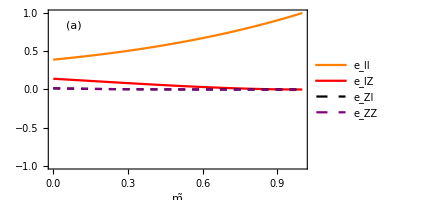

```mathematica
Plot[Evaluate[DeleteCases[Flatten[Abs[PTAdwm]^2],0]],{m,0,1},Frame->True,BaseStyle->14,
(*PlotRange->plotrangeamplitudes,*)
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{0,-1},
FrameLabel->{"m̃",None},
PlotStyle->{Orange,{Red},{Black,Dashed},{Purple,Dashed}},
PlotLegends->legend[{"e_II","e_IZ","e_ZI","e_ZZ"},{0.7,0.23},LegendLayout->{"Row",2}],
Epilog->Text["(a)",Scaled[{0.1,0.9}]]]
```

## Chapter plots

### Pulse temporal shape plots

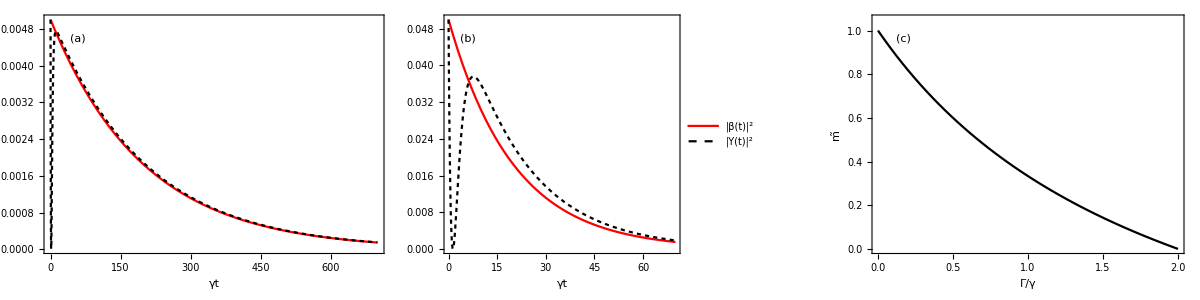

```mathematica
Grid[{{fig1a,fig1b,fig1c}}]
Export[overleafPath<>"Chap5Fig1.pdf",%];
```

### Average fidelity

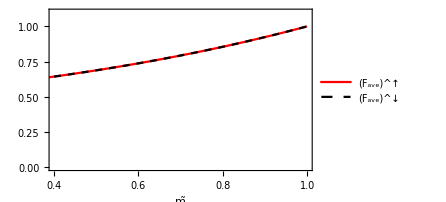

```mathematica
Plot[{averagefidelityup,averagefidelitydw},{m,0,1},
PlotStyle->{Red,{Black,Dashed}},
PlotRange->{{0.4,1},{0,1.1}},
PlotLegends->legend[{"(F_ave)^↑ ","(F_ave)^↓"},{0.75,0.23},LegendLayout->{"Row",2}],
FrameLabel->{"m̃",None}]
Export[overleafPath<>"AverageFidelities.pdf",%];
```

### Error matrix PTA

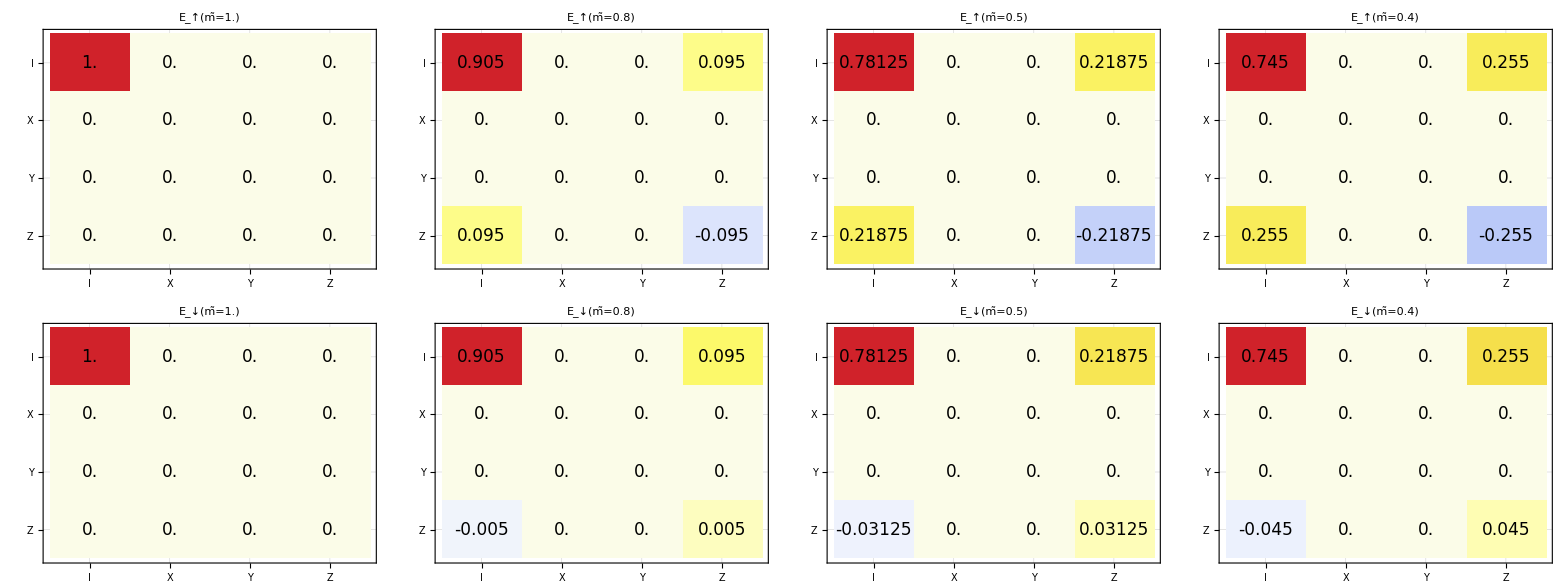

```mathematica
DecompositionXYFrameTick={{1,"I"},{2,"X"},{3,"Y"},{4,"Z"}};
AllTicks={DecompositionXYFrameTick,DecompositionXYFrameTick,None,None};
LowerRowTicks={DecompositionXYFrameTick,DecompositionXYFrameTick,None,None};

Grid[{Table[MatrixPlot[PTAupm/. m->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->AllTicks,PlotTheme->"Business",
PlotLabel->Style["E_↑(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],
Epilog->Table[Text[Style[PTAupm[[i,j]]/. m->x//N,17],{j-0.5,Length[PTAupm]-i+0.5}],{i,Length[PTAupm]},{j,Length[PTAupm[[i]]]}]],{x,{1.0,0.8,0.5,0.4}}],

Table[MatrixPlot[PTAdwm/. m->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->LowerRowTicks,
PlotTheme->"Business",
PlotLabel->Style["E_↓(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],Epilog->Table[Text[Style[PTAdwm[[i,j]]/. m->x//N,17],{j-0.5,Length[PTAdwm]-i+0.5}],{i,Length[PTAdwm]},{j,Length[PTAdwm[[i]]]}]],{x,{1.0,0.8,0.5,0.4}}]}]
Export[overleafPath<>"HintonDiagramErrorPTA.pdf",%];
```

### Non-null components of PTA

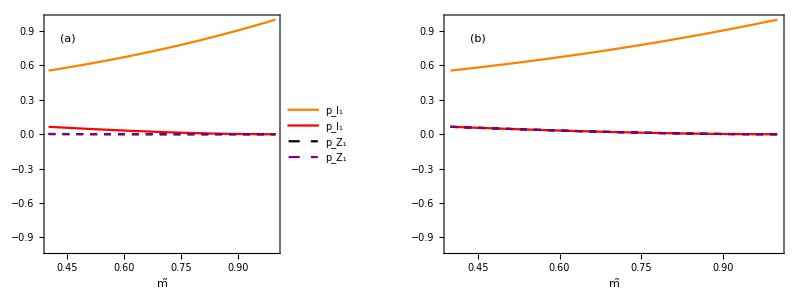

```mathematica
Grid[{{Plot[Evaluate[DeleteCases[Flatten[Abs[PTAdwm]^2],0]],{m,0.4,1},Frame->True,BaseStyle->14,
(*PlotRange->plotrangeamplitudes,*)
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{0.4,-1},
FrameLabel->{"m̃",None},
PlotStyle->{Orange,{Red},{Black,Dashed},{Purple,Dashed}},
PlotLegends->legend[{"p_I_1","p_I_1","p_Z_1","p_Z_1"},{0.7,0.23},LegendLayout->{"Row",2}],
Epilog->Text["(a)",Scaled[{0.1,0.9}]]],

Plot[Evaluate[DeleteCases[Flatten[Abs[PTAupm]^2],0]],{m,0.4,1},Frame->True,BaseStyle->14,
(*PlotRange->plotrangeamplitudes,*)
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{0.4,-1},
FrameLabel->{"m̃",None},
PlotStyle->{Orange,{Red},{Black,Dashed},{Purple,Dashed}},
(*PlotLegends->legend[{"e_II","e_IZ","e_ZI","e_ZZ"},{0.7,0.23},LegendLayout->{"Row",2}],*)
Epilog->Text["(b)",Scaled[{0.1,0.9}]]
(*Epilog->AlphabetLabelling["c"]*)]}}
]
Export[overleafPath<>"NonVanishingComponentsPTA.pdf",%];
```

### Real and imaginary parts of the real angles

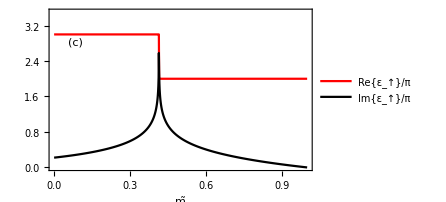

```mathematica
angleerrorUpPlot=ListLinePlot[{realparError,imaginaryparError},
PlotStyle->{{Red},{Black}},
PlotRange->{All,{0,3.5}},
PlotLegends->legend[{"Re{ε_↑}/π","Im{ε_↑}/π"},{0.8,0.35}],
FrameLabel->{"m̃",None},
Epilog->Text["(c)",Scaled[{0.1,0.8}]]]
Export[overleafPath<>"angleerrorUpPlot.pdf",angleerrorUpPlot];
```

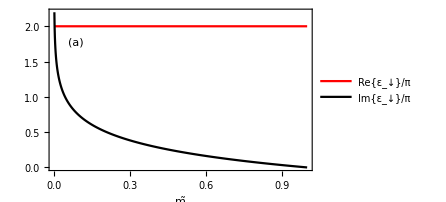

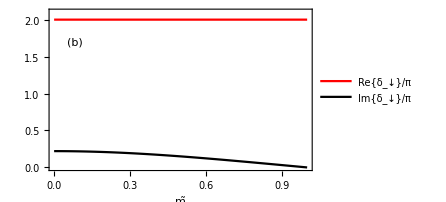

```mathematica
angleerrorDwPlot=ListLinePlot[{realparErrorDw,imaginaryparErrorDw},
PlotStyle->{{Red},{Black}},
PlotLegends->legend[{"Re{ε_↓}/π","Im{ε_↓}/π"},{0.8,0.35}],
FrameLabel->{"m̃",None},
Epilog->Text["(a)",Scaled[{0.1,0.8}]]]
anotherUnitaryerrorDwPlot=ListLinePlot[{realparAnotherUnitaryErrorDw,imaginaryparAnotherUnitaryErrorDw},
PlotStyle->{{Red},{Black}},
PlotRange->{All,{0,2.1}},
PlotLegends->legend[{"Re{δ_↓}/π","Im{δ_↓}/π"},{0.8,0.35}],
FrameLabel->{"m̃",None},
Epilog->Text["(b)",Scaled[{0.1,0.8}]]]
Export[overleafPath<>"anotherUnitaryerrorDwPlot.pdf",anotherUnitaryerrorDwPlot];
```

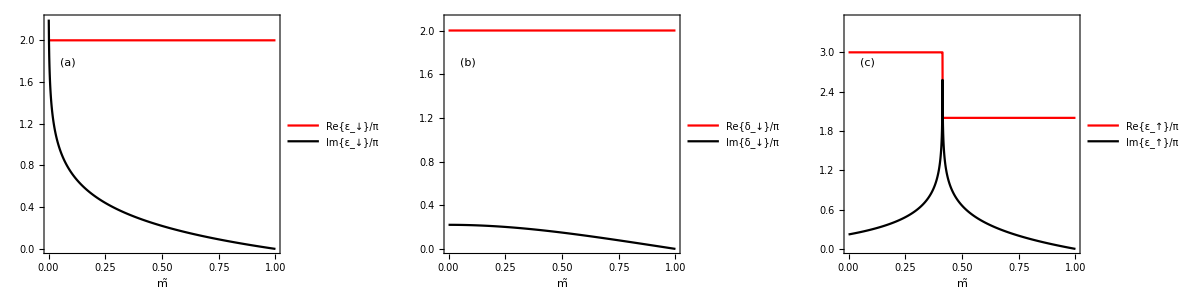

```mathematica
Grid[{{angleerrorDwPlot,anotherUnitaryerrorDwPlot,angleerrorUpPlot}}]
Export[overleafPath<>"GatesErrorsRealandImaginaryParts.pdf",%];
```

In Figure (a), we observe that the real part of ε↓ε↓​ remains constant at 2π2π throughout, while the imaginary part emerges as mm approaches 0, leading to an induced error. In Figure (b), the real part of δ↓δ↓​ also remains constant at 2π2π for all mm, and the imaginary part appears with a much smaller magnitude than 2π2π as mm approaches 0, becoming a constant error for m<0.4m<0.4. In Figure (c), we find that to achieve the desired CZ-gate, i.e., −Exp[iε↑]=−1−Exp[iε↑​]=−1, the mm-parameter must exceed 0.4; otherwise, the real part becomes 3π3π, resulting in the identity gate, −Exp[iε↑]=1−Exp[iε↑​]=1. Focusing on the region where m>0.4m>0.4, we successfully implement the desired CZ-gate, as the real part of ε↑ε↑​ is 2π2π. The error is unitary when m=1m=1 (monochromatic output), yielding the desired gate. For 0.4<m<10.4<m<1, the imaginary part comes into play, causing a tilt in the gate.

```mathematica
leakageDw=Tr[GdwrealOriginal†.GdwrealOriginal]/4//cf
leakageUp=Tr[GuprealOriginal†.GuprealOriginal]/4//cf
```

1/16 (3+m^2)^2

1/16 (13+m (2+m) (-2+m (2+m)))

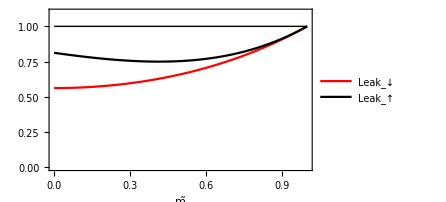

```mathematica
leakagePlots=Plot[{leakageDw,leakageUp},{m,0,1},
PlotStyle->{{Red},{Black}},
PlotRange->{All,{0,1.1}},
PlotLegends->legend[{"Leak_↓","Leak_↑"},{0.8,0.35}],
FrameLabel->{"m̃",None},
Epilog->{{Gray},Line[{{0,1},{1,1}}]}]
Export[overleafPath<>"Non-unitarity.pdf",%];
```

## Sketch zone

```mathematica
sol=Flatten@Solve[ⅇ^(- ⅈ ϵ)== (m^2+1)/2,ϵ]
```

{ϵ→ConditionalExpression[ⅈ (2 ⅈ π C[1]+Log[1/2 (1+m^2)]), C[1]∈ℤ]}

```mathematica
Exp[-ⅈ (ϵ/.sol//cf)]/.m->1//cf
```

ConditionalExpression[1, C[1]∈ℤ]

```mathematica
sol2=Flatten@Solve[ⅇ^(- ⅈ ϵ)== (m^2+2m-1)/2,ϵ]//cf
```

{ϵ→ConditionalExpression[-2 π C[1]+ⅈ Log[1/2 (-1+m (2+m))], C[1]∈ℤ]}

```mathematica
Exp[-ⅈ (ϵ/.sol2//cf)]/.m->1//cf
```

ConditionalExpression[1, C[1]∈ℤ]

```mathematica
Uideal=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}});
```

```mathematica
Uerror=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, ⅇ^(-ⅈ ϵ)}})//cf;
```

```mathematica
ρther = Eye[4]/4//mf
```

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4)

```mathematica
FullSimplify[ComplexExpand[Tr[Uideal†.Upaper]*Tr[Uideal†.Upaper]*]]
```

2+4 √((-1+𝔼1)^2)+2 Cos[δ]+8 ((-1+𝔼1)^2)^(1/4) Cos[δ/2] Cos[1/2 (δ-Arg[1-𝔼1])]

```mathematica
FullSimplify@ComplexExpand@Tr[Upaper†.Upaper]
```

2 (1+√((-1+𝔼1)^2)+√(𝔼1^2))

```mathematica
Fave = 1/20(2 (1+√((-1+𝔼1)^2)+√(𝔼1^2))+2+4 √((-1+𝔼1)^2)+2 Cos[δ]+8 ((-1+𝔼1)^2)^(1/4) Cos[δ/2] Cos[1/2 (δ-Arg[1-𝔼1])])//cf
```

1/10 (2+𝔼1+3 Abs[-1+𝔼1]+Cos[δ]+4 √Abs[-1+𝔼1] Cos[δ/2] Cos[1/2 (δ-Arg[1-𝔼1])])

```mathematica
Series[Fave,{δ,0,2},{𝔼1,0,2}]
```

1/10 (3 Abs[-1+𝔼1]+4 √Abs[-1+𝔼1] Cos[1/2 Arg[1-𝔼1]]+(3+𝔼1+O[𝔼1]^3))+1/5 √Abs[-1+𝔼1] Sin[1/2 Arg[1-𝔼1]] δ+1/20 (-1-2 √Abs[-1+𝔼1] Cos[1/2 Arg[1-𝔼1]]) δ^2+O[δ]^3

```mathematica
Tr[Uerror.ρther]/.ϵ->-1/2//N
```

0.969396+0.119856 ⅈ

```mathematica
Tr[Uerror.ρther]/.ϵ->1//N
```

0.885076-0.210368 ⅈ

```mathematica
Tr[Uerror]
```

3+ⅇ^(-ⅈ ϵ)

```mathematica
Uerror†.Uerror//cf
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Uerror.Uerror†//cf
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Upaper=({{1, 0, 0, 0}, {0, √(1-𝔼1), √𝔼1 ⅇ^(ⅈ ϕ), 0}, {0, -√𝔼1 ⅇ^(-ⅈ ϕ), √(1-𝔼1), 0}, {0, 0, 0, -ⅇ^(ⅈ δ)}});
```

```mathematica
Upaper.ρther//mf;
```

(1/4 | 0 | 0 | 0
0 | (√(1-𝔼1))/4 | 1/4 ⅇ^(ⅈ ϕ) √𝔼1 | 0
0 | -1/4 ⅇ^(-ⅈ ϕ) √𝔼1 | (√(1-𝔼1))/4 | 0
0 | 0 | 0 | -ⅇ^(ⅈ δ)/4)

```mathematica
tr=Tr[Upaper.ρther]
```

1/4-ⅇ^(ⅈ δ)/4+(√(1-𝔼1))/2

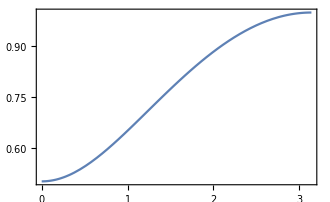

```mathematica
Plot[Abs[tr/.𝔼1->0],{δ,0,π}]
```

```mathematica
tr/.𝔼1->0/.δ->π/2
```

3/4-ⅈ/4

```mathematica
V=Upaper.Inverse[Uideal]//mf;
```

(1 | 0 | 0 | 0
0 | √(1-𝔼1) | ⅇ^(ⅈ ϕ) √𝔼1 | 0
0 | -ⅇ^(-ⅈ ϕ) √𝔼1 | √(1-𝔼1) | 0
0 | 0 | 0 | ⅇ^(ⅈ δ))

```mathematica
Tr[V]
```

1+ⅇ^(ⅈ δ)+2 √(1-𝔼1)

```mathematica
Tr[Upaper]
```

1-ⅇ^(ⅈ δ)+2 √(1-𝔼1)

```mathematica
Tr@Inverse[Uideal]
```

2

We define the ordered Pauli basis:

```mathematica
ℬ = Table[kron[i,j],{i,{σ0,σx,σy,σz}},{j,{σ0,σx,σy,σz}}]//mf;
```

((1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)
(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)
(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1))

```mathematica
decomposition = Table[Tr[ℬ⟦i,j⟧.V]/4,{i,1,4},{j,1,4}]//cf//mf;
```

(1/4 (1+ⅇ^(ⅈ δ)+2 √(1-𝔼1)) | 0 | 0 | 1/4 (1-ⅇ^(ⅈ δ))
0 | 1/2 ⅈ √𝔼1 Sin[ϕ] | -1/2 ⅈ √𝔼1 Cos[ϕ] | 0
0 | 1/2 ⅈ √𝔼1 Cos[ϕ] | 1/2 ⅈ √𝔼1 Sin[ϕ] | 0
1/4 (1-ⅇ^(ⅈ δ)) | 0 | 0 | 1/4 (1+ⅇ^(ⅈ δ)-2 √(1-𝔼1)))

```mathematica
Tr[decomposition]//cf
```

1/2 (1+ⅇ^(ⅈ δ)+2 ⅈ √𝔼1 Sin[ϕ])

```mathematica
pz = decomposition[[1,4]]decomposition[[1,4]]*//cf
```

1/8 (1-Cos[δ])

```mathematica
Series[pz,{δ,0,2}]
```

δ^2/16+O[δ]^3

```mathematica
pxx =decomposition[[2,3]]decomposition[[2,3]]*//cf
```

1/4 𝔼1 Cos[ϕ]^2

```mathematica
pxy =decomposition[[2,2]]decomposition[[2,2]]*//cf
```

1/4 𝔼1 Sin[ϕ]^2

```mathematica
pzz =FullSimplify@ComplexExpand[decomposition[[4,4]]decomposition[[4,4]]*]
```

1/8 (1+2 √((-1+𝔼1)^2)+Cos[δ]-4 ((-1+𝔼1)^2)^(1/4) Cos[δ/2] Cos[1/2 (δ-Arg[1-𝔼1])])

```mathematica
approximation1 = Assuming[𝔼1<1,Series[pzz,{𝔼1,0,2},{δ,0,2}]]//cf
```

(δ^2/16+O[δ]^3)+(-δ^2/16+O[δ]^3) 𝔼1+(1/16-δ^2/64+O[δ]^3) 𝔼1^2+O[𝔼1]^3

```mathematica
approximation2 = Series[1/4 (2-2 √(1-𝔼1)-𝔼1)+1/8 (-1/2+√(1-𝔼1)) δ^2,{𝔼1,0,3}]//cf
```

δ^2/16-(δ^2 𝔼1)/16+1/64 (4-δ^2) 𝔼1^2+1/128 (4-δ^2) 𝔼1^3+O[𝔼1]^4

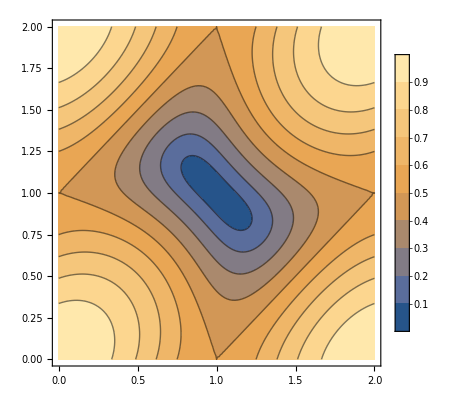

```mathematica
ListContourPlot[Flatten[Table[{ϵdw/π,δdw/π,Abs[PTAdw[[1,1]]]},{ϵdw,0,2π,π/60},{δdw,0,2π,π/60}],1],PlotLegends->Automatic]
```

```mathematica
testreal=({{1, 𝔼1/2, 0, 𝔼1^2/4}, {0, ((1-m)+𝔼1)/2, 0, ((1+m)𝔼1)/4}, {0, 0, 1/2, (1-m)/4}, {0, 0, 0, (1+m^2)/4}})//cf;
```

```mathematica
testreal/.𝔼1->0/.m->1//mf
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | 1/2)

{{1,0,0,0},{0,0,0,0},{0,0,1/2,0},{0,0,0,1/2}}

```mathematica
up=Basis[2,1]//mf;
dw=Basis[2,2]//mf;
```

(1
0)

(0
1)

```mathematica
MatrixExp[-ⅈ π/4 σy].dw==(-up+dw)/(√2)
```

True

```mathematica
MatrixExp[-ⅈ π/4 σy].up==(up+dw)/(√2)
```

True